# Cardinal Fall Launch

```mathematica
cardinalFall2024 = Import["C:\\Users\\brend\\OneDrive\\Desktop\\School\\Extracurricular\\HPR\\Cardinal\\Fall 2024\\AtmoData\\cardinal_Fall2024.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
startTime = 425000;
endTime = 535000;
```

```mathematica
msToSec[ms_] := DecimalForm[ms/1000];
msToMin[ms_] := DecimalForm[ms/60000];
timeSec = msToSec/@Normal[cardinalFall2024[All, "time (ms)"]];
timeMin = msToMin/@Normal[cardinalFall2024[All, "time (ms)"]];
```

```mathematica
cardinalFall2024
```

Dataset[<>]

## Plot Data

Temperature over time

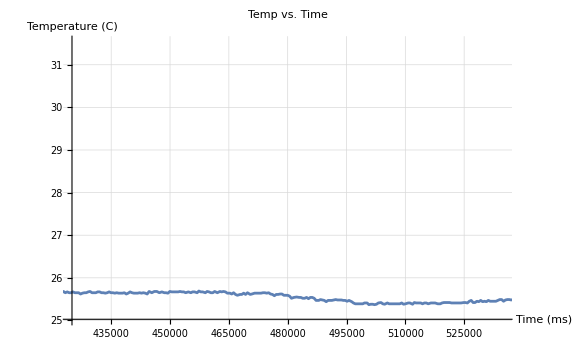

```mathematica
ListPlot[Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "temperature (C)"]]}],
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Temp vs. Time", AxesLabel->{"Time (ms)","Temperature (C)"},
PlotRange->{{startTime,endTime},Automatic}]
```

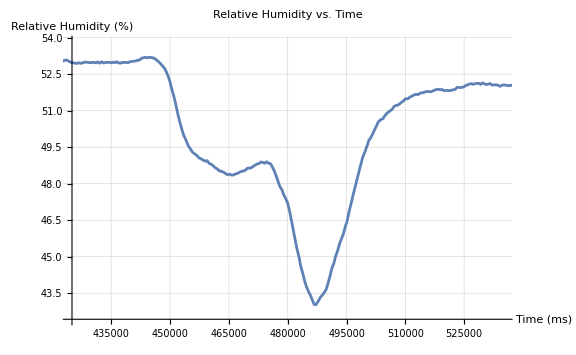

```mathematica
ListPlot[Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "humidity (%)"]]}],
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Relative Humidity vs. Time", AxesLabel->{"Time (ms)","Relative Humidity (%)"},
PlotRange->{{startTime,endTime},Automatic}]
```

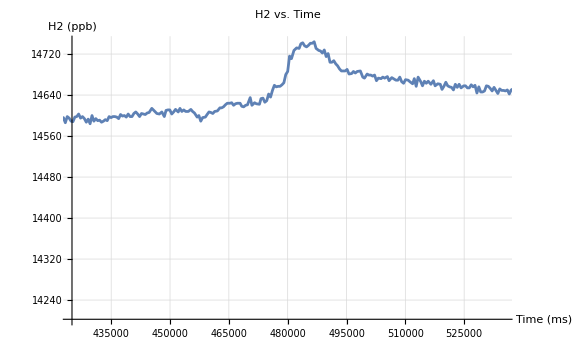

```mathematica
ListPlot[Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "h2 (ppb)"]]}],
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"H2 vs. Time", AxesLabel->{"Time (ms)","H2 (ppb)"},
PlotRange->{{startTime,endTime},Automatic}]
```

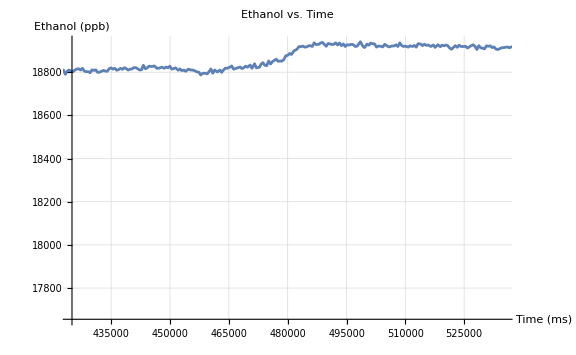

```mathematica
ListPlot[Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "ethanol (ppb)"]]}],
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Ethanol vs. Time", AxesLabel->{"Time (ms)","Ethanol (ppb)"},
PlotRange->{{startTime,endTime},Automatic}]
```

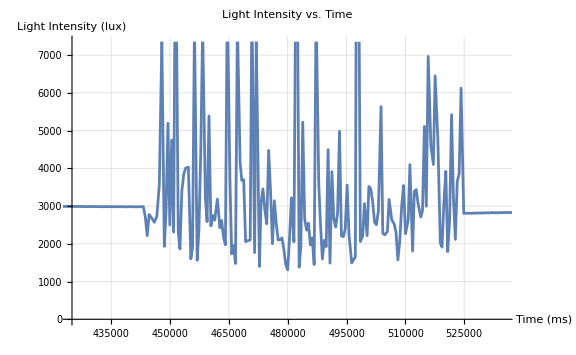

```mathematica
ListPlot[Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "lux"]]}],
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Light Intensity vs. Time", AxesLabel->{"Time (ms)","Light Intensity (lux)"},
PlotRange->{{startTime,endTime},{0, Automatic}}]
```

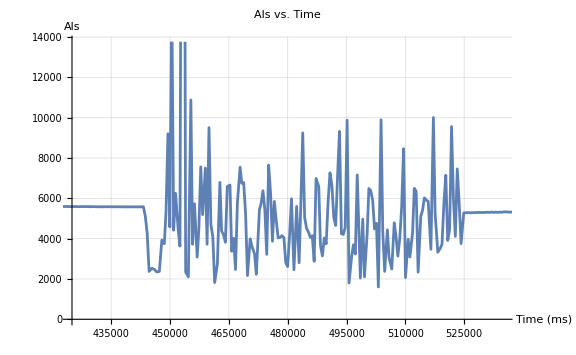

```mathematica
ListPlot[Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "als"]]}],
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Als vs. Time", AxesLabel->{"Time (ms)","Als"},
PlotRange->{{startTime,endTime},{0, Automatic}}]
```

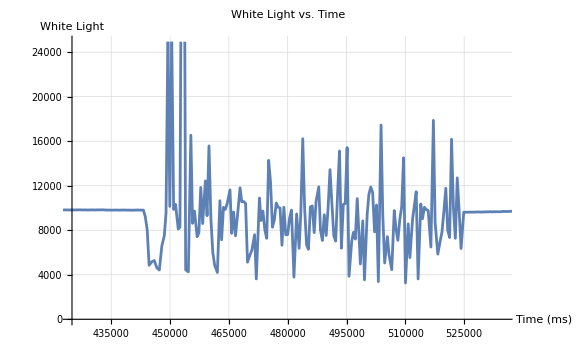

```mathematica
ListPlot[Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "white"]]}],
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"White Light vs. Time", AxesLabel->{"Time (ms)","White Light"},
PlotRange->{{startTime,endTime},{0, Automatic}}]
```

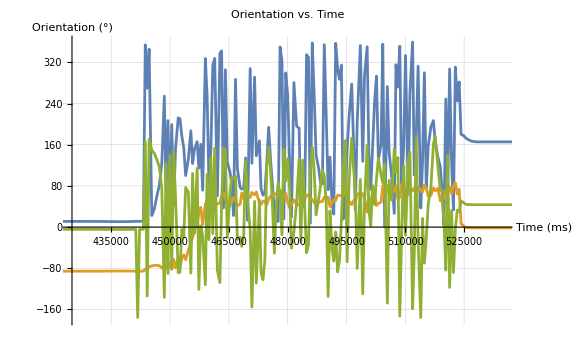

```mathematica
ListPlot[{
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "ori_x (m/s^2)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "ori_y (m/s^2)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "ori_z (m/s^2)"]]}]
},
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Orientation vs. Time", AxesLabel->{"Time (ms)","Orientation (°)"},
PlotRange->{{startTime,endTime},{Min[{Min[Normal[cardinalFall2024[All, "ori_x (m/s^2)"]]],Min[Normal[cardinalFall2024[All, "ori_y (m/s^2)"]]], Min[Normal[cardinalFall2024[All, "ori_z (m/s^2)"]]]}], 
Max[{Max[Normal[cardinalFall2024[All, "ori_x (m/s^2)"]]],Max[Normal[cardinalFall2024[All, "ori_y (m/s^2)"]]], Max[Normal[cardinalFall2024[All, "ori_z (m/s^2)"]]]}]}
}]
```

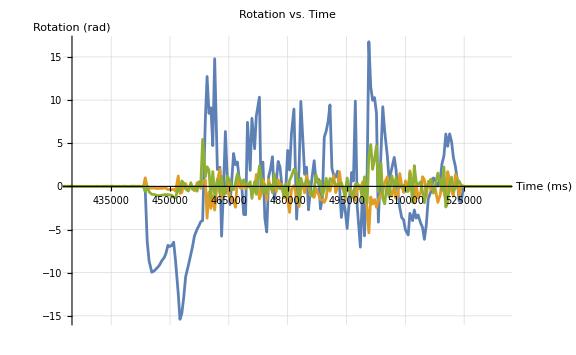

```mathematica
ListPlot[{
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "gyro_x (rad)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "gyro_y (rad)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "gyro_z (rad)"]]}]
},
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Rotation vs. Time", AxesLabel->{"Time (ms)","Rotation (rad)"},
PlotRange->{{startTime,endTime},{Min[{Min[Normal[cardinalFall2024[All, "gyro_x (rad)"]]],Min[Normal[cardinalFall2024[All, "gyro_y (rad)"]]], Min[Normal[cardinalFall2024[All, "gyro_z (rad)"]]]}], 
Max[{Max[Normal[cardinalFall2024[All, "gyro_x (rad)"]]],Max[Normal[cardinalFall2024[All, "gyro_y (rad)"]]], Max[Normal[cardinalFall2024[All, "gyro_x (rad)"]]]}]}
}]
```

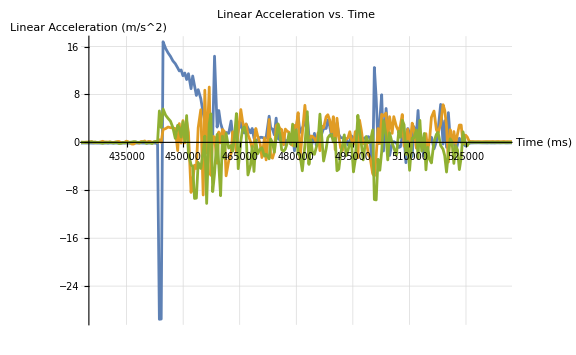

```mathematica
ListPlot[{
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "linear_x (m/s^2)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "linear_y (m/s^2)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "linear_z (m/s^2)"]]}]
},
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Linear Acceleration vs. Time", AxesLabel->{"Time (ms)","Linear Acceleration (m/s^2)"},
PlotRange->{{startTime,endTime},{Min[{Min[Normal[cardinalFall2024[All, "linear_x (m/s^2)"]]],Min[Normal[cardinalFall2024[All, "linear_y (m/s^2)"]]], Min[Normal[cardinalFall2024[All, "linear_y (m/s^2)"]]]}], 
Max[{Max[Normal[cardinalFall2024[All, "linear_x (m/s^2)"]]],Max[Normal[cardinalFall2024[All, "linear_y (m/s^2)"]]], Max[Normal[cardinalFall2024[All, "linear_x (m/s^2)"]]]}]}
}]
```

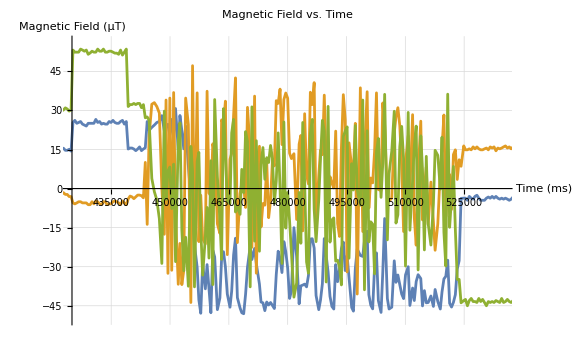

```mathematica
ListPlot[{
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "magnetic_x (?T)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "magnetic_y (?T)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "magnetic_z (?T)"]]}]
},
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Magnetic Field vs. Time", AxesLabel->{"Time (ms)","Magnetic Field (µT)"},
PlotRange->{{startTime,endTime},{Min[{Min[Normal[cardinalFall2024[All, "magnetic_x (?T)"]]],Min[Normal[cardinalFall2024[All, "magnetic_y (?T)"]]], Min[Normal[cardinalFall2024[All, "magnetic_z (?T)"]]]}], 
Max[{Max[Normal[cardinalFall2024[All, "magnetic_x (?T)"]]],Max[Normal[cardinalFall2024[All, "magnetic_y (?T)"]]], Max[Normal[cardinalFall2024[All, "magnetic_z (?T)"]]]}]}
}]
```

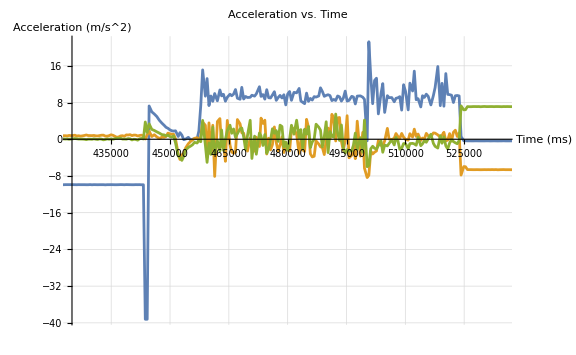

```mathematica
ListPlot[{
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "acceleration_x (m/s^2)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "acceleration_y (m/s^2)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "acceleration_z (m/s^2)"]]}]
},
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Acceleration vs. Time", AxesLabel->{"Time (ms)","Acceleration (m/s^2)"},
PlotRange->{{startTime,endTime},{Min[{Min[Normal[cardinalFall2024[All, "acceleration_x (m/s^2)"]]],Min[Normal[cardinalFall2024[All, "acceleration_y (m/s^2)"]]], Min[Normal[cardinalFall2024[All, "acceleration_z (m/s^2)"]]]}], 
Max[{Max[Normal[cardinalFall2024[All, "acceleration_x (m/s^2)"]]],Max[Normal[cardinalFall2024[All, "acceleration_y (m/s^2)"]]], Max[Normal[cardinalFall2024[All, "acceleration_z (m/s^2)"]]]}]}
}]
```

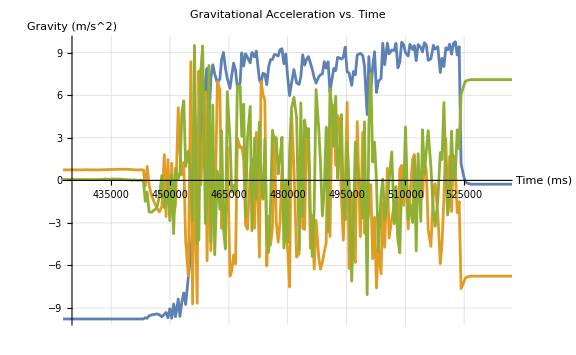

```mathematica
ListPlot[{
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "gravity_x (m/s^2)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "gravity_y (m/s^2)"]]}],
Transpose[{Normal[cardinalFall2024[All, "time (ms)"]], Normal[cardinalFall2024[All, "gravity_z (m/s^2)"]]}]
},
Joined->True,GridLines->Automatic, ImageSize->Large,
PlotLabel->"Gravitational Acceleration vs. Time", AxesLabel->{"Time (ms)","Gravity (m/s^2)"},
PlotRange->{{startTime,endTime},{Min[{Min[Normal[cardinalFall2024[All, "gravity_x (m/s^2)"]]],Min[Normal[cardinalFall2024[All, "gravity_y (m/s^2)"]]], Min[Normal[cardinalFall2024[All, "gravity_z (m/s^2)"]]]}], 
Max[{Max[Normal[cardinalFall2024[All, "gravity_x (m/s^2)"]]],Max[Normal[cardinalFall2024[All, "gravity_y (m/s^2)"]]], Max[Normal[cardinalFall2024[All, "gravity_z (m/s^2)"]]]}]}
}]
```